# Asteroid Blastwave

The  equation for the pressure blast wave generated by the asteroid is given by:

(Equation in latex)
This is a simple Friedlander equation
Plotting a singular blast wave:

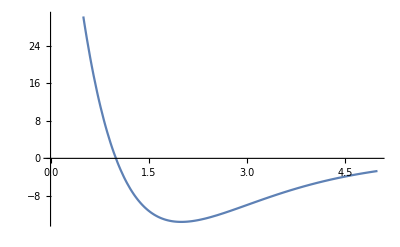

```mathematica
(*inital variables*)
t1 = 1;
pinital= 100;
Plot[pinital* E^(-t/t1)* (1- t/t1), {t, 0, 5}]
```

Now we want to do the same for intensity

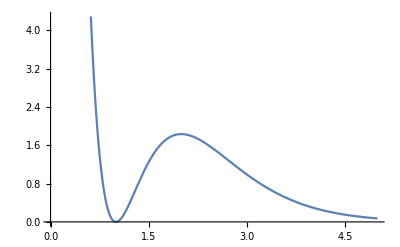

```mathematica
t1 = 1;
i0 = 100;
Remove[f]
f[t_]:=i0 * (E^(-t/t1)(1-t/t1))^2;
Plot[f[t], {t, 0,5}]
```

Now we want to graph the actual equation, in steps. Since I don’t fully understand the equation, I will graph the simplest versions, and then add onto it as I go step by step. For simplicity, we’re only going to do pressure.

Graphing the first equation, assuming peak pressure, arrival time of blast,  and arrival time at zero crossing are all some kind of constant. We will also ignore the summation for now. Since t_i is given as “arrival time from blast” and t_1i is “’t_1’ from fragment at position x = zero crossing time for P(t,x) = 0, We can just say t - t_i is just t

The equation is given by:

P(t,x̄) = P_(0_i)(x̄) ⅇ^((-(t-t_i(x)))/(t_(1i)(x)))[1 - (t-t_i(x))/(t_(1i)(x))]

```mathematica
Manipulate[Plot[pinital* E^(-(t )/ti)* (1- (t )/ti), {t, 0, 10}], {{pinital,100, "Pressure Initial"}, 50, 150}, {{ti,1,"Time Initial"}, 0.4, 5}]
```

We now want to include the peak pressure from fragment i at position x. To do this, we will use another formula mentioned earlier in the equation sheet involving peak overpressure in section 11.  We will vary Energy in this instance. The Equation is given by:
p(r) = p_n [ r (Ε_kt^(-1/3)()])^α_n + p_f[r (Ε_kt^(-1/3))]^α_f

```mathematica
pn = 3.11 * 10^11;
an = -2.95;
ti = 1;
pf = 1.8*10^7;
af = -1.13;
g= Sqrt[x^2 + y^2];
en = 1;
po= pn*(g*en^(-1/3))^an + pf*(g*en^(-1/3))^af
Remove[en]
Manipulate[Plot3D[po* E^(-(t)/ti)* (1- (t)/ti),{x,-10,10},{y,-10,10}],{{t,0.4, "Time"},0.4,5}, {en, 0,1}]
```

(3.11×10^11)/((x^2+y^2)^1.475)+(1.8×10^7)/((x^2+y^2)^0.565)

```mathematica
pn = 3.11 * 10^11;
an = -2.95;
ti = 1;
pf = 1.8*10^7;
af = -1.13;
g= Sqrt[x^2 + y^2];
en = 1;
po= pn*(g*en^(-1/3))^an + pf*(g*en^(-1/3))^af
Remove[en]
Manipulate[Plot3D[(pn*(g*en^(-1/3))^an + pf*(g*en^(-1/3))^af)* E^(-(t)/ti)* (1- (t)/ti),{x,-5,5},{y,-5,5}, PlotRange->{-10^11,10^11}],{{t,0.4, "Time"},0.4,5}, {{en, 1, "Arbitrary Energy"}, 0,10}]
```

(3.11×10^11)/((x^2+y^2)^1.475)+(1.8×10^7)/((x^2+y^2)^0.565)